## FitEllipse-example.nb FitEllipse, PrimaryAxes

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 17:19:18
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

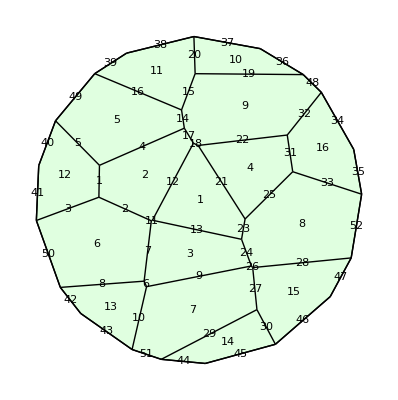

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True, "EdgeNumbers"-> True]
```

```mathematica
v6=CellVertexCoordinates[w,6]
```

{{-99.2158,-12.4994},{-84.5412,-53.4115},{-33.2469,-49.5988},{-28.8281,-12.6822},{-60.9322,1.72033}}

```mathematica
FitEllipse[v6]
```

{Angle→3.07962,Axes→{33.8822,27.0644},Graphics→-Graphics-}

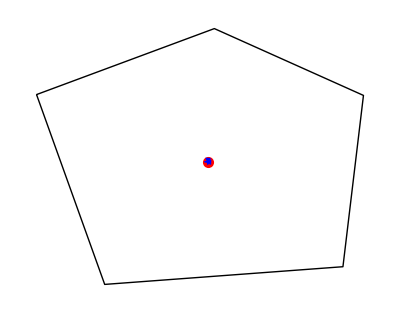
{Vectors→{{{-62.3223,-27.0111},{-63.1022,-26.9627}},{{-62.3223,-27.0111},{-62.361,-27.634}}},Graphics→-Graphics-,Eigenvalues→{0.781334,0.624113},Angles→{3.07962,-1.63277}}

```mathematica
PrimaryAxes[v6]
```

```mathematica
v=CellVertexCoordinates[w];
```

```mathematica
Show[("Graphics"/.FitEllipse[#])&/@v]
```

-Graphics-